## 实验四、随机数学实验

### 例1：模拟随机事件。

现有 n 套钥匙和锁分离的锁具，每把钥匙恰能打开一把锁。某人随机选取一把钥匙依次试开所有锁，直至所有钥匙和锁配对。求试开次数 X 的分布。

```mathematica
f[x_]:=Module[{i,j,n},
n=Length[x];Sum[Min[x⟦i⟧-Sum[Boole[x⟦j⟧<x⟦i⟧],{j,i-1}],n-i],{i,n}]
];
```

{{7,2},{8,14},{9,52},{10,142},{11,314},{12,598},{13,1016},{14,1566},{15,2218},{16,2912},{17,3562},{18,4066},{19,4346},{20,4344},{21,4058},{22,3526},{23,2824},{24,2072},{25,1376},{26,800},{27,384},{28,128}}

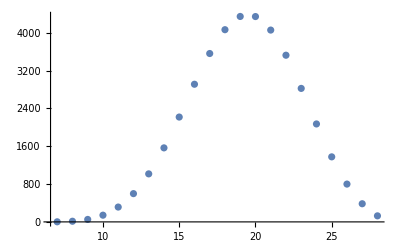

```mathematica
n=8;p=Permutations[Range[n]];q=Sort[Tally[Table[f[x],{x,p}]]]
ListPlot[q]
```

思考：求 X 的分布列的准确值，以及 n→∞ 的极限分布。

思考：设计一种试开流程，使得试开次数 X 的均值最小。

把一根线段任意折成三段，求它们构成三角形的概率。

```mathematica
f1[]:=Module[{a,b,c,x},
x=Sort[RandomReal[1,2]];{a,b,c}=Sort[{x⟦1⟧,x⟦2⟧-x⟦1⟧,1-x⟦2⟧}];Boole[a+b>c]
];
0.00001Sum[f1[],{100000}]
```

```mathematica
f2[]:=Module[{a,b,c},
a=RandomReal[];a=Min[a,1-a];b=(1-a)RandomReal[];{a,b,c}=Sort[{a,b,1-a-b}];Boole[a+b>c]
];
0.00001Sum[f2[],{100000}]
```

思考：上述两种解法的结果为何不同？哪个正确？

在正方形的外接圆内随机选取一点，求点在正方形内的概率。

```mathematica
f1[]:=Module[{r,s},
r=Sqrt[2]RandomReal[];s=2π RandomReal[];Boole[r*Abs[Cos[s]]≤1&&r*Abs[Sin[s]]≤1]
];
0.00001Sum[f1[],{100000}]
```

```mathematica
f2[]:=Module[{x,y},
{x,y}=RandomReal[{-2,2},2];While[x^2+y^2>2,{x,y}=RandomReal[{-2,2},2]];Boole[Abs[x]≤1&&Abs[y]≤1]
];
0.00001Sum[f2[],{100000}]
```

思考：上述两种解法的结果为何不同？哪个正确？

### 例2：中心极限定理。

```mathematica
f[n_]:=Module[{a=0,b=1,x},x=RandomReal[UniformDistribution[{a,b}],n];(Total[x]-0.5(a+b)n)/((b-a)√(n/12))];
```

```mathematica
f[n_]:=Module[{p=0.5,x},x=RandomInteger[BernoulliDistribution[p],n];(Total[x]-n p)/(√(n p(1-p)))];
```

```mathematica
n=10;Show[Histogram[Table[f[n],{10000}],Automatic,"ProbabilityDensity"],Plot[(ⅇ^(-x^2/2))/(√(2 π)),{x,-3,3}]]
```

思考：“连续分布的中心极限”比“离散分布的中心极限”更容易收敛？

由中心极限定理可得 (X_1+⋯+X_n)/n≈N(E(X),1/n D(X))，其中 X_1,⋯,X_n 独立同分布。

```mathematica
n=10^6;s=0;Do[{x,y}=RandomReal[1,2];If[x^2+y^2<1,s++],{n}];p=π/4;{s/n-p,√((p (1-p))/n)}//N
```

### 例3：用均匀分布构造分布。

```mathematica
(*指数分布*)x=Table[-Log[RandomReal[]],{10^6}];Histogram[x,PlotLabel->{Mean[x],Variance[x]}]
```

```mathematica
(*正态分布*)x=Table[√(-2 Log[RandomReal[]]) Cos[2 π RandomReal[]],{10^6}];Histogram[x,PlotLabel->{Mean[x],Variance[x]}]
```

思考：设∫_(-∞)^∞ p(x)dx=1。构造连续型随机变量 X，其密度函数为 p (x)。

```mathematica
(*Bernoulli分布*)p=0.3;x=Table[Boole[RandomReal[]<p],{10^6}];Sort[Tally[x]]
```

```mathematica
(*几何分布*)p=0.2;x=Table[Floor[Log[1-p,RandomReal[]]],{10^6}];Histogram[x,PlotLabel->N[{Mean[x],Variance[x]}]]
```

```mathematica
(*Poisson分布*)Clear[Poisson];
Poisson[λ_]:=Module[{k,r,s,t},
r=Exp[λ]RandomReal[];s=t=1.0;k=0;While[s<r,k++;t*=λ/k;s+=t];k
];
x=Table[Poisson[2],{10^6}];Histogram[x,PlotLabel->N[{Mean[x],Variance[x]}]]
```

思考：设∑_(k=-∞)^∞ p_k=1。构造离散型随机变量 X，满足 Prob(X=k)=p_k，∀k∈ℤ。

### 例4：多元正态分布的性质。

设 A 是实方阵，随机向量 X~ N(0,Σ)，则 A X~N(0,A Σ A^T)。

```mathematica
a=RandomReal[{-1,1},{2,2}];x=Table[a.RandomReal[NormalDistribution[],2],{10^6}];
Histogram3D[x,AxesLabel->{"x","y"}]
ParametricPlot[a.{Cos[t],Sin[t]},{t,0,2Pi}]
x1=x⟦All,1⟧;x2=x⟦All,2⟧;
{Variance[x1],Variance[x2],Covariance[x1,x2],a.Transpose[a]//MatrixForm}
```

设 P 是正交阵，随机向量 X~ N(0,I_n)，Y=X/(√(X_1^2+⋯+X_n^2))，则 P Y 与 Y 同分布。由此可得，Y 是单位球面 S^(n-1)上的均匀分布。

```mathematica
x=Table[Arg[RandomReal[NormalDistribution[],2].{1,ⅈ}],{100}];ListPlot[Sort[x]]
```

```mathematica
x=Table[Normalize[RandomReal[NormalDistribution[],3]],{1000}];Graphics3D[Point[x]]
```

思考：如何检验球面上的点列是否分布均匀？

设随机向量 X 服从正态分布，则每个 X_k 服从正态分布。对于其他分布 X,Y，结论不一定成立。
例如：设 (X,Y)服从单位圆盘上的均匀分布。(1)求 X 的分布。(2) X 与 Y 是否独立？是否相关？

```mathematica
f[]:=Module[{x=1,y=1},While[x^2+y^2>1,{x,y}=RandomReal[{-1,1},2]];{x,y}];
{x,y}=Transpose[Table[f[],{10^6}]];Histogram[x]
Covariance[x,y]
```

思考：把本例中的单位圆盘换成一般区域 D，把均匀分布换成一般分布 p(x,y)，结论如何？

设 X,Y 均服从正态分布，则 X 与 Y 独立⇔X 与 Y 不相关。对于其他分布 X,Y，结论不一定成立。

```mathematica
a=RandomReal[2 π,{10^6}];x=Cos[a];y=Sin[a];Covariance[x,y]
```

思考：对于什么样的分布 F，设 X,Y 均服从 F，则 X 与 Y 独立⇔X 与 Y 不相关？

### 例5：随机变量的参数估计。

已知 X 服从均匀分布 U (a,b)，估计其参数 a,b。

```mathematica
{a,b}=Sort[RandomReal[{-10,10},2]];x=Sort[RandomReal[{a,b},100]]
```

方法1：E(X)=(a+b)/2，D(X)=(b-a)^2/12    ⇒    a,b=E(X)±√(3D(X))

```mathematica
{{1,-1},{1,1}}.{Mean[x],√(3 Variance[x])}
```

方法2：a≈Min_(1≤k≤n)X_k，b≈Max_(1≤k≤n)X_k

```mathematica
{Min[x],Max[x]}
```

方法3：E(Min_(1≤k≤n)X_k)=(n a+b)/(n+1)，E(Max_(1≤k≤n)X_k)=(a+n b)/(n+1)    ⇒    a≈(n Min-Max)/(n-1),b≈(n Max-Min)/(n-1)

```mathematica
1/(n-1){{n,-1},{-1,n}}.{Min[x],Max[x]}
```

方法4：E(X)=(a+b)/2，E(Max_(1≤k≤n)X_k-Min_(1≤k≤n)X_k)=(n-1)/(n+1)(b-a)    ⇒    a,b≈E(X)±(n+1)/(2(n-1))(Max-Min)

```mathematica
{{1,-(n+1)/(2(n-1))},{1,(n+1)/(2(n-1))}}.{Mean[x],Max[x]-Min[x]}
```

思考：上述哪种方法比较好？证明你的结论。给出其他更好的估计方法。

### 例6：观察随机过程的性质。

Poisson过程。x_k 表示第 k 个事件发生的时间，λ 是单位时间内的平均事件数。

```mathematica
λ=0.3;n=10;t=0;
x=Table[t+=RandomReal[ExponentialDistribution[λ]],{n}]
p=Prepend[Table[{x⟦i⟧,i},{i,n}],{0,0}];Show[ListLinePlot[p,InterpolationOrder->0],Graphics[{PointSize[Large],Point[p]}]]
```

设旅客到达车站是参数 λ 的Poisson过程，列车在时刻 T 离站。观察时间段[0,T]中旅客的总等待时间 X。

```mathematica
f[λ_,T_]:=Module[{n,s,t},
n=s=0;t=RandomReal[ExponentialDistribution[λ]];
While[t<T,n++;s+=T-t;t+=RandomReal[ExponentialDistribution[λ]]];s
];
```

```mathematica
λ=RandomReal[];T=100;x=Table[f[λ,T],{10000}];Histogram[x,PlotLabel->{λ,T}]
```

思考：求 X 的密度函数。

随机游动。动点在每个时刻以 1/4 的概率向上、下、左、右平移单位距离。观察动点的轨迹。

```mathematica
u={{1,0},{0,1},{-1,0},{0,-1}};n=10000;p={0,0};
x=Join[{p},Table[p+=u⟦RandomInteger[{1,4}]⟧,{n}]];
Graphics[{Line[x],PointSize[Large],Blue,Point[x⟦1⟧],Red,Point[x⟦-1⟧]}]
```

```mathematica
(*动点在第n时刻的位置*)Clear[f1];f1[n_]:=Sum[u⟦RandomInteger[{1,4}]⟧,{n}];
```

```mathematica
x=Table[f1[100],{10000}];Histogram3D[x]
```

思考：动点在第 n 时刻的位置服从什么分布？

```mathematica
(*动点在前n时刻经过的不同点的数目*)Clear[f2];f2[n_]:=Module[{p},
p={0,0};Length[Union[Table[p+=u⟦RandomInteger[{1,4}]⟧,{n}]]]
];
```

```mathematica
x=Table[f2[100],{10000}];Histogram[x]
```

思考：当 n→∞时，(f2(n))/n→^(a.s.)1/2？

自回归序列 X_0=ϵ_0，⋯，X_(k-1)=ϵ_(k-1)，X_n=c_1 X_(n-1)+⋯+c_k X_(n-k)+ϵ_n，∀n≥k，其中{ϵ_n|n∈ℕ}是白噪声序列。

```mathematica
k=3;c=RandomReal[{-1,1},k-1];AppendTo[c,1-Total[c]];c
```

```mathematica
n=1000;x=RandomReal[{-1,1},n];Do[x⟦i⟧+=Sum[c⟦j⟧ x⟦i-j⟧,{j,k}],{i,k+1,n}];ListLinePlot[x]
```

思考：{X_n|n∈ℕ}具有哪些性质？{X_n|n 充分大}是否受 X_0,⋯,X_(k-1)影响？能否由{X_n}确定 k 和 c_1,⋯,c_k？